This notebook generates spliced-read performance plots for a given sample. REQUIRES UNIX-BASED OS. Enter the directory where “.perform” files may be found below.

```mathematica
(*Set Apple colors -- from http://mathematica.stackexchange.com/questions/38722/discrete-colordata-scheme-with-n-colors*)
```

```mathematica
blue=RGBColor[17.6/100,41.6/100,63.1/100];
green=RGBColor[34.9/100,66.7/100,33.3/100];
yellow=RGBColor[96.9/100,68.6/100,20.8/100];
red=RGBColor[86.3/100,13.3/100,19.6/100];
purple=RGBColor[55.3/100,27.5/100,55.7/100];
grey=RGBColor[55.7/100,57.3/100,56.9/100];
apple7={blue,Orange,red,yellow, purple,grey, green};
```

```mathematica
SetDirectory["/Users/anellore/paper_perform"];
```

```mathematica
(*Select sample*)
```

```mathematica
sampleNames={"NA18508.1.M_111124_1","NA18861.1.M_120209_2"}
```

{NA18508.1.M_111124_1,NA18861.1.M_120209_2}

```mathematica
(*Read pro files for coverage*)
```

```mathematica
TPMs=Table[Import[sampleNames[[i]]~~"_sim.pro"][[All, {6,10}]], {i, 1, 2}];
```

```mathematica
(*Compute TPMs*)
```

```mathematica
For[j=1, j≤2, j+=1,For[i=1, i≤2, i+=1,TPMs[[j]][[All, i]] =N[TPMs[[j]][[All, i]] / Total[TPMs[[j]][[All, i]]]]*10^6]];
```

```mathematica
sortedOriginalTPMs=Table[Reverse[Sort[Transpose[TPMs[[i]]][[1]]]], {i, 1, 2}];
```

```mathematica
sortedSimTPMs = Table[Reverse[Sort[Transpose[TPMs[[i]]][[2]]]], {i, 1, 2}];
```

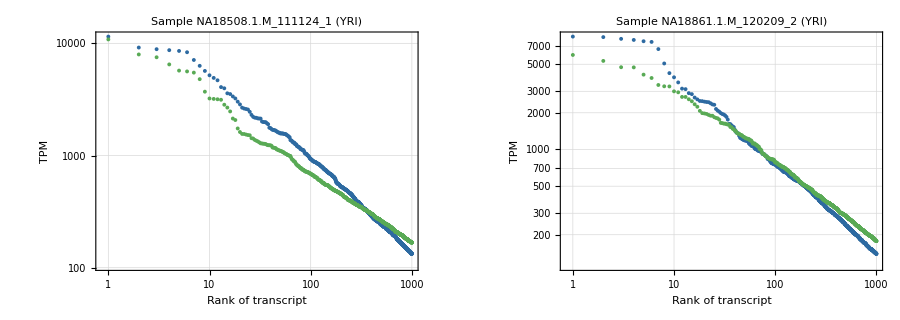

```mathematica
TPMPlot =Legended[GraphicsGrid[{Table[ListLogLogPlot[{sortedOriginalTPMs[[i]][[Range[1,1000]]], sortedSimTPMs[[i]][[Range[1,1000]]]}, PlotRange->All, Frame->True,FrameLabel->{"Rank of transcript","TPM"},PlotTheme->{"Detailed"},PlotStyle->apple7,PlotLabel->Style["Sample "~~sampleNames[[i]]~~" (YRI)", FontFamily->"Palatino", FontSize->13],FrameStyle->{Directive[FontFamily->"Palatino", FontSize->18,Black], Directive[FontFamily->"Palatino", FontSize->18]}, PlotStyle->PointSize[.007]], {i, 1,2}]},PlotLabel->Style["TPMs for GEUVADIS sample-Flux simulation pairs", 24, FontFamily->"Futura"],Frame->All, FrameStyle->Directive[Dashed,Gray],ImageSize->{900,320}], LineLegend[{Red,Green,Blue},{"red","green","blue"}]]
```

```mathematica
ColorData[7]
```

ColorDataFunction[…]

```mathematica
ColorData["NeonColors"]
```

ColorDataFunction[…]

```mathematica
SwatchLegend[3,Range[4]]
```

```mathematica
Correlation[sampleCoverage[[All,1]], sampleCoverage[[All,2]]]
```

0.885803

```mathematica
sampleCoverage[[All, {6,9}]]
```

{{4,3.49995×10^-7},{0,0.},{0,0.},{0,0.},{1,0.},{3,0.},{0,0.},{0,0.},{0,0.},{1,1.99997×10^-7},{0,0.},{0,0.},{0,0.},183023,{0,0.},{0,0.},{0,0.},{1,1.49998×10^-7},{0,0.},{5,5.49993×10^-7},{0,0.},{6,2.49997×10^-7},{0,0.},{0,0.},{4,1.49998×10^-7},{4,3.49995×10^-7},{0,0.}}
 |  |  |  |

```mathematica
performanceFiles = DeleteCases[Select[FileNames["*"],(StringFreeQ[#,"summary"]&)], StringFreeQ[#,sampleName]&]
```

{NA18508.1.M_111124_1.rail.perform,NA18508.1.M_111124_1.star.ann_paired_1pass.perform,NA18508.1.M_111124_1.star.ann_paired_2pass.perform,NA18508.1.M_111124_1.star.ann_single_1pass.perform,NA18508.1.M_111124_1.star.ann_single_2pass.perform,NA18508.1.M_111124_1.star.noann_paired_1pass.perform,NA18508.1.M_111124_1.star.noann_paired_2pass.perform,NA18508.1.M_111124_1.star.noann_single_1pass.perform,NA18508.1.M_111124_1.star.noann_single_2pass.perform,NA18508.1.M_111124_1.tophat.ann_paired.perform,NA18508.1.M_111124_1.tophat.ann_single.perform,NA18508.1.M_111124_1.tophat.noann_paired.perform,NA18508.1.M_111124_1.tophat.noann_single.perform,NA18861.1.M_120209_2.rail.perform,NA18861.1.M_120209_2.star.ann_paired_1pass.perform,NA18861.1.M_120209_2.star.ann_paired_2pass.perform,NA18861.1.M_120209_2.star.ann_single_1pass.perform,NA18861.1.M_120209_2.star.ann_single_2pass.perform,NA18861.1.M_120209_2.star.noann_paired_1pass.perform,NA18861.1.M_120209_2.star.noann_paired_2pass.perform,NA18861.1.M_120209_2.star.noann_single_1pass.perform,NA18861.1.M_120209_2.star.noann_single_2pass.perform,NA18861.1.M_120209_2.tophat.ann_paired.perform,NA18861.1.M_120209_2.tophat.ann_single.perform,NA18861.1.M_120209_2.tophat.noann_paired.perform,NA18861.1.M_120209_2.tophat.noann_single.perform}

```mathematica
verboseNameRules = {sampleName~~".rail.perform"->"Rail-RNA", sampleName~~".star.ann_paired_1pass.perform"->"STAR 1-pass paired ann", sampleName~~".star.ann_paired_2pass.perform"->"STAR 2-pass paired ann", sampleName~~".star.noann_paired_1pass.perform"->"STAR 1-pass paired", sampleName~~".star.noann_paired_2pass.perform"->"STAR 2-pass paired",
sampleName~~".star.ann_single_1pass.perform"->"STAR 1-pass single ann", sampleName~~".star.ann_single_2pass.perform"->"STAR 2-pass single ann", sampleName~~".star.noann_single_1pass.perform"->"STAR 1-pass single", sampleName~~".star.noann_single_2pass.perform"->"STAR 2-pass single", sampleName~~".tophat.ann_paired.perform"->"TopHat paired ann", sampleName~~".tophat.ann_single.perform"->"TopHat single ann",
sampleName~~".tophat.noann_paired.perform"->"TopHat paired",
sampleName~~".tophat.noann_single.perform"->"TopHat single"};
```

```mathematica
getPosition[x_]:=Position[performanceFiles,s_String/;StringMatchQ[s,x]][[1,1]]
```

```mathematica
(*parameter varied here is upper bound on lowest true coverage ("true" as in "from simulated alignments") from among introns overlapped by read*)
```

```mathematica
statsAtTrueCoverage[x_, y_] :=Import[StringReplace["!awk '{for (i = 1; i <= threshold; i++){ if ($5 == i) {rel[i] += $1; ret[i] += $2; if ($1 == $2) {relret[i] += $1}}}} END {for (i = 1; i <= threshold; i++) {printf \"%d\\t%d\\t%d\\n\",rel[i],ret[i],relret[i]}}' filename", {"filename"->x,"threshold"->ToString[y]}], "TSV"]
```

```mathematica
statsAboveRetrievedCoverage[x_, y_] :=Import[StringReplace["!awk '{for (i = 1; i <= threshold; i++){ if ($8 >= i) {rel[i] += $1; ret[i] += $2; if ($1 == $2) {relret[i] += $1}}}} END {for (i = 1; i <= threshold; i++) {printf \"%d\\t%d\\t%d\\n\",rel[i],ret[i],relret[i]}}' filename", {"filename"->x,"threshold"->ToString[y]}], "TSV"]
```

```mathematica
(*Up to coverage 100 should be enough to get good plots*)
```

```mathematica
allTrueStats=(statsAtTrueCoverage[#, 100]&)/@performanceFiles;
```

```mathematica
allRetrieved = (statsAboveRetrievedCoverage[#, 100]&)/@performanceFiles;
```

```mathematica
recallPrecisionFromStats[x_] :=
{N[x[[3]] / x[[1]]], N[x[[3]] / x[[2]]]}
```

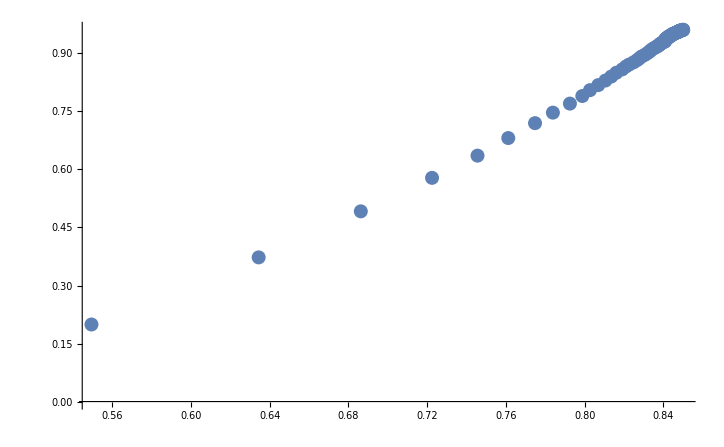

```mathematica
ListPlot[recallPrecisionFromStats/@mystats, PlotRange->All]
```